```mathematica
distanceCSV=Import["https://raw.githubusercontent.com/HALtheWise/POE-lab2/master/docs/zeroPassDistances.csv","Csv"];
distanceData=distanceCSV[[2;;Length[distanceCSV]-1]];
```

```mathematica
line = Fit[distanceData, {1,x,x^2,x^3},x]
Fit[Map[Reverse,distanceData], {1,x,x^2,x^3},x]
```

782.774-15.9408 x+0.128033 x^2-0.000356379 x^3

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

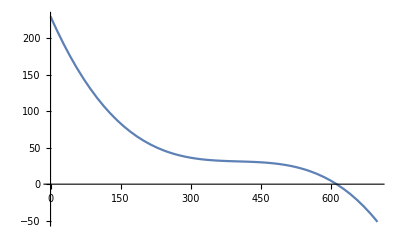

```mathematica
Plot[230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3,{x,0,700}]
```

```mathematica
voltageToDistance[x_]=(230.1430411867322-1.4451995839029892 x+0.0035444572391777783 x^2-2.9360497052173657*^-6 x^3)
```

230.143-1.4452 x+0.00354446 x^2-2.93605×10^-6 x^3

```mathematica
plotLine=Plot[line,{x,5,200},PlotRange->{{0,200},{0,700}}];
plotData=ListPlot[distanceData,PlotRange->{{0,150},{0,600}}];
```

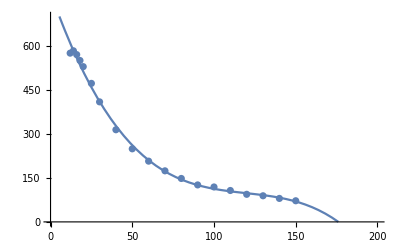

```mathematica
Show[plotLine,plotData]
```

```mathematica
serial=DeviceOpen["Serial",{"/dev/ttyUSB1","BaudRate"->19200}]
```

DeviceObject[…]

```mathematica
DeviceReadBuffer[serial,50]
```

{51,50,55,13,10,51,51,51,13,10,51,48,54,13,10,50,55,48,13,10,50,53,54,13,10,50,56,48,13,10,51,49,56,13,10,51,52,49,13,10,51,50,53,13,10,50,56,54,13,10}

```mathematica
Dynamic[voltageToDistance[ToExpression[FromCharacterCode[DeviceReadBuffer[serial,"ReadTerminator"->10]]]]]
```

```mathematica
FromCharacterCode[{50,51,52}]
```

234

```mathematica
ToExpression["234"]
```

234

```mathematica
line
```

782.774-15.9408 x+0.128033 x^2-0.000356379 x^3

```mathematica
DeviceReadBuffer[serial,4]
```

DeviceReadBuffer::ncdev: $Failed is not open.

$Failed

```mathematica
serial["Properties"]
```

$Failed[Properties]

```mathematica
DeviceReadLatest[serial]
```

DeviceReadLatest::ncdev: $Failed is not open.

DeviceReadLatest[$Failed]

```mathematica
DeviceClose[serial]
```

DeviceClose::ncdev: $Failed is not open.

$Failed